```mathematica
unitCell[x_,y_]:={Orange,Disk[{x,y},0.1],Lighter[Blue],Disk[{x,y+2/3 Sin[120 Degree]},0.1],Gray,
,Line[{{x,y},{x,y+2/3 Sin[120 Degree]}}],Line[{{x,y},{x+Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],Line[{{x,y},{x-Cos[30 Degree]/2,y-Sin[30 Degree]/2}}]}
```

```mathematica
Graphics[unitCell[0,0],ImageSize->100]
```

-Graphics-

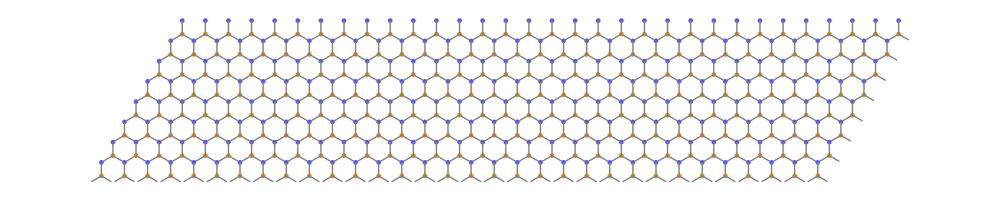

```mathematica
Graphics[
Block[
{unitVectA={-Cos[120 Degree],Sin[120 Degree]}
,unitVectB={1,0}
},Table[
unitCell@@(unitVectA j+unitVectB k)
,{j,1,8}
,{k,1, 32}]
],ImageSize->1000
]
```